```mathematica
GetIdFromGraph[g_]:=Block[{},
FromDigits[
Flatten[
Table[
Table[
If[EdgeQ[g,i<->j ],1,0]
,
{j,i+1, VertexCount[g]}
],
{i,1, VertexCount[g]}
]
],
3]
]
```

```mathematica
GetIdFromGraph[allGraphs5[lambdaKey,"graph"]]
```

20665

```mathematica
lambdaKey
```

20665

```mathematica
EmbedGraph[master_,key_,vertices_]:=Block[
{val=allGraphs5[key], sets, reference=vertices, g, sub, edge},
sets=val["vertexsets"];
g=master;
(* delete existing edges *)
Table[
Table[
edge=vertices[[i]]<->vertices[[j]];
If[EdgeQ[g,edge],
g = EdgeDelete[g,edge]
]
,{j,i+1,5}
]
,{i,1,5}
];
(* contract vertices if needed *)
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];

sub=val["graph"];
(* add edges *)
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}
];
g
]
```

```mathematica
Monitor[Table[allGraphs2[k,"chromial"]=ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}],k];
```

```mathematica
Monitor[Table[allGraphs3[k,"chromial"]=ChromaticPolynomial[allGraphs3[k,"graph"],x],{k,Keys[allGraphs3]}],k];
```

```mathematica
Monitor[Table[allGraphs4[k,"chromial"]=ChromaticPolynomial[allGraphs4[k,"graph"],x],{k,Keys[allGraphs4]}],k];
```

```mathematica
Monitor[Table[allGraphs5[k,"chromial"]=ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,Keys[allGraphs5]}],k];
```

```mathematica
Clear[CalcChromial];
```

```mathematica
CalcChromial[g_,pos_:""]:=Block[{vertices, subGraph,id,index,prefix,h,subresult},
If[pos=="",prefix="",prefix=ToString[pos]<>"."];
If[CompleteGraphQ[g]||, 
ChromaticPolynomial[g,x]
,
If[VertexCount[g]<5,

,
id=K5Key;
While[id==K5Key,
vertices = VertexList[g];
vertices=RandomSample[vertices,5];
subGraph=Subgraph[g,vertices];
id = GetIdFromGraph[subGraph];
];
index=0;
Total[
Table[
h=EmbedGraph[g,fullId,vertices];
subresult=CalcChromial[h,prefix<>ToString[index]];
Print[ {prefix<>ToString[index]->ShowGraph5Least[fullId],subresult, ChromaticPolynomial[h,x]}];
index++;,

subresult
,
{fullId,(ListofVars[allGraphs5[id,"colofour"]]/.RepKey["C"])}
]
]
]
]
]
```

```mathematica
GetIdFromGraph[CycleGraph[4]]
```

280

```mathematica
Keys[allGraphs4[280]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
allGraphs4[280,"graph"]
```

-Graphics-

```mathematica
CalcChromial[CycleGraph[6]]//CompleteBaseCoeff//Timing
```

{0→-Graphics-383080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{1→-Graphics-382810,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{2→-Graphics-368980,x-2 x^2+x^3,x-2 x^2+x^3}

{3→-Graphics-368170,-2 x+5 x^2-4 x^3+x^4,-2 x+5 x^2-4 x^3+x^4}

{4→-Graphics-361660,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{5→-Graphics-361120,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{6.0→-Graphics-560111,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{6.1→-Graphics-492070,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{6.2→-Graphics-361660,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{6.3→-Graphics-361120,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{6.4→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{6.5→-Graphics-297670,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{6.6→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{6.7→-Graphics-295510,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{6.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{6→-Graphics-360850,-4 x^2+8 x^3-5 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{7→-Graphics-319840,x-2 x^2+x^3,x-2 x^2+x^3}

{8→-Graphics-319540,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{9→-Graphics-317380,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{10→-Graphics-317140,-2 x+5 x^2-4 x^3+x^4,-2 x+5 x^2-4 x^3+x^4}

{11.0→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{11.1→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{11.2→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{11→-Graphics-317110,12 x-28 x^2+23 x^3-8 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{12→-Graphics-305861,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{13→-Graphics-304961,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{14→-Graphics-303340,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{15→-Graphics-302621,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{16.0→-Graphics-382810,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{16.1→-Graphics-361660,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{16.2→-Graphics-360860,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{16.3→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{16.4→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{16.5→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{16.6→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{16.7→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{16.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{16→-Graphics-302530,-4 x^2+8 x^3-5 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{17→-Graphics-298571,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{18→-Graphics-297970,-2 x+5 x^2-4 x^3+x^4,-2 x+5 x^2-4 x^3+x^4}

{19.0→-Graphics-492100,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{19.1→-Graphics-492070,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{19.2→-Graphics-297970,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{19.3→-Graphics-297670,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{19.4→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{19.5→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{19.6→-Graphics-295510,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{19.7→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{19.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{19→-Graphics-297670,-4 x^2+8 x^3-5 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{20→-Graphics-296080,-2 x+5 x^2-4 x^3+x^4,-2 x+5 x^2-4 x^3+x^4}

{21.0→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{21.1→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{21.2→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{21→-Graphics-296050,12 x-28 x^2+23 x^3-8 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{22→-Graphics-295600,-4 x+8 x^2-5 x^3+x^4,-4 x+8 x^2-5 x^3+x^4}

{23.0→-Graphics-317140,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{23.1→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{23.2→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{23.3→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{23.4→-Graphics-295371,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{23.5→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{23.6→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{23.7→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{23.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{23→-Graphics-295510,-4 x^2+8 x^3-5 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{24.0→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{24.1→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{24.2→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{24→-Graphics-295330,12 x-28 x^2+23 x^3-8 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5}

{25.0→-Graphics-382810,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.1→-Graphics-361660,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.2→-Graphics-360860,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.3→-Graphics-360850,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.4→-Graphics-317140,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.5→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.6→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.7→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.8→-Graphics-295371,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{25.9→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.10→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.11→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{25.12→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{25→-Graphics-295270,-2 x^2+5 x^3-4 x^4+x^5,6 x-17 x^2+17 x^3-7 x^4+x^5}

{26.0→-Graphics-368170,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.1→-Graphics-361120,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.2→-Graphics-360860,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.3→-Graphics-360850,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.4.0→-Graphics-317140,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.4.1→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.4.2→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.4.3→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.4.4→-Graphics-295371,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.4.5→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.4.6→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.4.7→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.4.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.4→-Graphics-302530,-4 x^2+8 x^3-5 x^4+x^5,18 x-39 x^2+29 x^3-9 x^4+x^5}

{26.5.0→-Graphics-317140,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.5.1→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.5.2→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.5.3→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.5.4→-Graphics-295371,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.5.5→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.5.6→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.5.7→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.5.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.5→-Graphics-295510,-4 x^2+8 x^3-5 x^4+x^5,18 x-39 x^2+29 x^3-9 x^4+x^5}

{26.6→-Graphics-295270,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.7.0→-Graphics-317140,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.7.1→-Graphics-317110,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.7.2→-Graphics-296080,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.7.3→-Graphics-296050,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.7.4→-Graphics-295371,2 x-3 x^2+x^3,2 x-3 x^2+x^3}

{26.7.5→-Graphics-295330,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.7.6→-Graphics-295270,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.7.7→-Graphics-295250,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.7.8→-Graphics-295240,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.7→-Graphics-295250,-4 x^2+8 x^3-5 x^4+x^5,18 x-39 x^2+29 x^3-9 x^4+x^5}

{26.8.0→-Graphics-317140,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.8.1→-Graphics-317110,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.8.2→-Graphics-296080,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.8.3→-Graphics-296050,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.8.4→-Graphics-295371,-6 x+11 x^2-6 x^3+x^4,-6 x+11 x^2-6 x^3+x^4}

{26.8.5→-Graphics-295330,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.8.6→-Graphics-295270,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.8.7→-Graphics-295250,24 x-50 x^2+35 x^3-10 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5}

{26.8.8→-Graphics-295240,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6}

{26.8→-Graphics-295240,-18 x+57 x^2-68 x^3+38 x^4-10 x^5+x^6,-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6}

{26→-Graphics-295240,12 x-22 x^2+8 x^3+6 x^4-5 x^5+x^6,-48 x+124 x^2-120 x^3+55 x^4-12 x^5+x^6}

{1.17188,{0,0,2,49,67,18,1}}

```mathematica
ChromaticPolynomial[CycleGraph[6],x]//CompleteBaseCoeff//Timing
```

{0.015625,{0,0,1,10,20,9,1}}

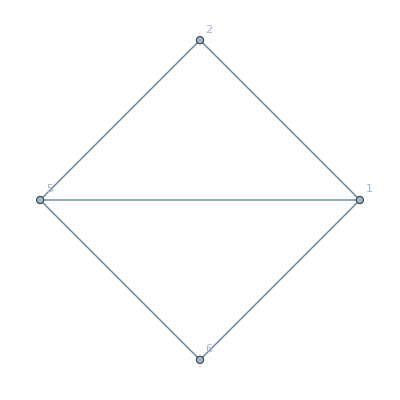

```mathematica
Graph[EmbedGraph[CycleGraph[6],alfa1Key,{1,2,3,4,5}], VertexLabels->"Name"]
```